Em uma cidade há 250 indústrias. Qual o tamanho mínimo da amostra (amostragem aleatória simples) para erro amostral de até 4%?

n_0=1/0.04^2=1/0.0016=625.
n=(250·625)/(250+625)=156250/875=150.

```mathematica
{0.04^2,1/0.0016,250*625,250*525/875}
```

{0.0016,625.,156250,150}

No estado de Santa Catarina existem 24.500 indústrias, qual o tamanho da amostra necessário para o mesmo erro (4%)?

n=(24500·625)/(24500+625)=15312500/25125=609.453.

```mathematica
{24500*625,24500+625,N@24500*625/(24500+625)}
```

{15312500,25125,609.453}

Na região Sul há 91.230 indústrias. Qual o tamanho da amostra para o mesmo erro (4%)?

n=(91230·625)/(91230+625)=620.747.

```mathematica
{91230*625,91230+625,N@91230*625/(91230+625)}
```

{57018750,91855,620.747}

Se no estado do Rio Grande do Sul se acumulam 35% das indústrias, “qual a solução mais adequada para realizar a amostragem” (considerando todos os dados)? Indique os valores a serem amostrados em cada estado para a solução indicada.

(35·91230)/100=28281.

To do.

```mathematica
{N@(31*91230)/100}
```

{28281.3}

50 amostras de água foi medida a quantidade de fluoreto, em mg/L, e obtida a distribuição:

Fluoreto | Frequência
[1.3; 1.4) | 3
[1.4; 1.5) | 9
[1.5; 1.6) | 15
[1.6; 1.7) | 10
[1.7; 1.8) | 8
[1.8; 1.9] | 5

[a; b) significa a pertence, b não pertence.

Determinar média e desvio-padrão.

x̄=(1.35·3+1.45·9+1.55·15+1.65·10+1.75·8+1.85·5)/(3+9+15+10+8+5)=1.602.

σ^2=[(1.35-1.602)^2·3+(1.45-1.602)^2·9+(1.55-1.602)^2·15+(1.65-1.602)^2·10+(1.75-1.602)^2·8+(1.85-1.602)^2·5]/50=0.18896.

s=√0.18896=0.137463.

```mathematica
{3+9+15+10+8+5,(1.35*3+1.45*9+1.55*15+1.65*10+1.75*8+1.85*5)/50,((1.35-1.602)^2*3+(1.45-1.602)^2*9+(1.55-1.602)^2*15+(1.65-1.602)^2*10+(1.75-1.602)^2*8+(1.85-1.602)^2*5)/50,√0.018896}
```

{50,1.602,0.018896,0.137463}

Definir um intervalo de 95% de confiança para a média populacional e expressar em palavras o significado deste intervalo.

(a,b)=x̄±Z_(α/2)·σ/(√n)={1.60+1.96·0.137463/50=1.60539
1.60-1.96·0.137463/50=1.5835.

```mathematica
{1.6+6*0.137463/50,1.6-6*0.137463/50}
```

{1.6165,1.5835}

(a,b)=x̄±t_(α,n-1)·(s(x))/(√n)={1.602+(1.676·0.137463)/(√50)=1.63458
1.602-(1.676·0.137463)/(√50)=1.56942.

O intervalo expressa que há 95% de confiança que o valor da média populacional se situa entre 1.56942 e 1.63458.

```mathematica
{1.602+(1.676*0.137463)/(√50),1.602-(1.676*0.137463)/(√50)}
```

{1.63458,1.56942}

Definir um intervalo de confiança de 95% para a proporção populacional de valores < 1.5 mg/L (observe que o fato descrito é monocaudal).

n=3+9+15+10+8+5=50.
p̂=(3+9)/n=0.24.
(a,b)=p̂±Z_α √((p̂ (1-p̂))/n)={0.24+3.92·√((0.24·0.76)/50)=0.476763
0.24-3.92·√((0.24·0.76)/50)=0.00323719.

```mathematica
{N@(3+9)/(3+9+15+10+8+5),N@4/20,3+9+15+10+8+5,N@12/50,N@0.24+3.92*√((0.24*0.76)/50),N@0.24-3.92*√((0.24*0.76)/50)}
```

{0.24,0.2,50,0.24,0.476763,0.00323719}

Pesados sete pacotes: 25.4, 25.2, 25.6, 25.3, 25.0, 25.4, 25.5 g. O desvio padrão inputado pela balança utilizada é de 0.3 g.

Determine os intervalos de confiança (para média) para probabilidades de 90% e 95%, expressando em palavras os seus significados.

x̄=(25.4+25.2+25.6+25.3+25.0+25.4+25.5)/7=25.3429.
σ^2=1/6((25.4-25.3429)^2+(25.2-25.3429)^2+(25.6-25.3429)^2+(25.3-25.3429)^2+(25.0-25.3429)^2+(25.4-25.3429)^2+(25.5-25.3429)^2)=0.0395238.

s=√0.0395238=0.198806.

s=0.3+√0.0395238=0.498806.

Para 90%:

(a,b)=25.3429±1.65·0.198806/(√7)=(25.4669,25.2189).

(a,b)=25.3429±1.65·0.498806/(√7)=(25.654,25.0318).

(a,b)=x̄±t_(α,n-1)·(s(x))/(√n)={25.3429+1.440·0.498806/(√7)=25.6144
25.3429-1.440·0.498806/(√7)=25.0714.

O intervalo significa que há 90% de confiança que o valor da média populacional se situe entre 25.0714 e 25.6144.

Para 95%:

(a,b)=25.3429±1.96·0.198806/(√7)=(25.4902,25.1956).

(a,b)=25.3429±1.96·0.498806/(√7)=(25.7124,24.9734).

(a,b)=x̄±t_(α,n-1)·(s(x))/(√n)={25.3429+1.943·0.498806/(√7)=25.7092
25.3429-1.943·0.498806/(√7)=24.9766.

O intervalo significa que há 95% de confiança que o valor da média populacional se situe entre 24.9766 e 25.7092.

```mathematica
{(25.4+25.2+25.6+25.3+25.0+25.4+25.5)/7,"μ"->Mean@{25.4,25.2,25.6,25.3,25.0,25.4,25.5},1/6((25.4-25.3429)^2+(25.2-25.3429)^2+(25.6-25.3429)^2+(25.3-25.3429)^2+(25.0-25.3429)^2+(25.4-25.3429)^2+(25.5-25.3429)^2),"σ^2"->Variance@{25.4,25.2,25.6,25.3,25.0,25.4,25.5},"σ"->0.3+√0.039523809523809614,"σ"->StandardDeviation@{25.4,25.2,25.6,25.3,25.0,25.4,25.5},25.3429+1.65*0.198806/(√7),25.3429-1.65*0.198806/(√7),25.3429+1.96*0.198806/(√7),25.3429-1.96*0.198806/(√7),0.198806+0.3,25.3429+1.65*0.498806/(√7),25.3429-1.65*0.498806/(√7),25.3429+1.96*0.498806/(√7),25.3429-1.96*0.498806/(√7),25.3429+1.440*0.498806/(√7),25.3429-1.440*0.498806/(√7),25.3429+1.943*0.498806/(√7),25.3429-1.943*0.498806/(√7)}
```

{25.3429,μ→25.3429,0.0395238,σ^2→0.0395238,σ→0.498806,σ→0.198806,25.4669,25.2189,25.4902,25.1956,0.498806,25.654,25.0318,25.7124,24.9734,25.6144,25.0714,25.7092,24.9766}

Desenhe os valores padronizados obtidos, pintando as áreas das probabilidades calculadas, em dois gráficos diferentes da distribuição normal, no GeoGebra em anexo.

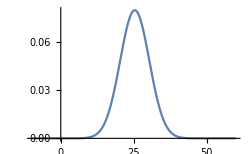
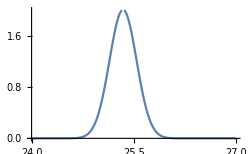

```mathematica
{Plot[PDF[NormalDistribution[25.3429,5],x],{x,-10,60},ImageSize->250],Plot[PDF[NormalDistribution[25.3429,0.198806],x],{x,24,27},ImageSize->250,PlotRange->{0,2}]}
```

Determine e explique qual dos intervalos é mais rigoroso.

O intervalo com 90% de confiança é mais rigoroso, pois é mais preciso (com menor amplitude) que o intervalo com 95% de confiança:
25.6144-25.0714=0.543<25.7092-24.9766=0.7326.

```mathematica
{25.4902-25.1956,25.4669-25.2189,25.654-25.0318,25.7124-24.9734,25.6144-25.0714,25.7092-24.9766}
```

{0.2946,0.248,0.6222,0.739,0.543,0.7326}

Medidas 12 peças: 194, 196, 193, 193, 195, 195, 197, 194, 195, 194, 196, 194 mm. Supondo distribuição normal:

Determinar os intervalos de confiança da média para 95%, expressando descritivamente os seus significados.

x̄=(194+196+193+193+195+195+197+194+195+194+196+194)/12=194.667.

σ^2=1/11((194-194.667)^2+(196-194.667)^2+(193-194.667)^2+(193-194.667)^2+(195-194.667)^2+(195-194.667)^2+(197-194.667)^2+(194-194.667)^2+(195-194.667)^2+(194-194.667)^2+(196-194.667)^2+(194-194.667^2)=1.51515.

s=√1.51515=1.23091.

(a,b)=x̄±t_(α,n-1)·(s(x))/(√n)={194.667+1.796·1.23091/(√12)=195.305
194.667-1.796·1.23091/(√12)=194.029.

O intervalo significa que há 95% de confiança que o valor da média populacional se situa entre 194.029 e 195.305.

```mathematica
{N@((194+196+193+193+195+195+197+194+195+194+196+194)/12),N@Mean@{194,196,193,193,195,195,197,194,195,194,196,194},
1/11((194-194.667)^2+(196-194.667)^2+(193-194.667)^2+(193-194.667)^2+(195-194.667)^2+(195-194.667)^2+(197-194.667)^2+(194-194.667)^2+(195-194.667)^2+(194-194.667)^2+(196-194.667)^2+(194-194.667)^2),N@Variance@{194,196,193,193,195,195,197,194,195,194,196,194},√1.51515,N@StandardDeviation@{194,196,193,193,195,195,197,194,195,194,196,194},194.667+1.96*1.23091/(√12),194.667-1.96*1.23091/(√12),194.667+1.796*1.23091/(√12),194.667-1.796*1.23091/(√12)}
```

{194.667,194.667,1.51515,1.51515,1.23091,1.23091,195.363,193.971,195.305,194.029}

Desenhar em gráfico da distribuição normal todos os “valores padronizados” obtidos, pintando as áreas das probabilidades. (O que é “valor padronizado”?)

Supondo um desvio padrão conhecido da média populacional de 0.7 mm, qual o intervalo de confiança de 95% da média populacional? Explique porquê a diferença para os intervalos calculados no primeiro item (sem desvio padrão conhecido) e qual o intervalo mais “apurado”.

(a,b)=x̄±z_(α/2)·σ/(√n)={194.667+1.96·0.7/(√12)=195.063
194.667-1.96·0.7/(√12)=194.271.

A diferença se dá porque a estatística da média possui incerteza maior em comparação ao parâmetro média, requerendo uma correção de probabilidade fornecida pela distribuição t-Student, com uma distribuição diferente de probabilidade para amostras pequenas.
O intervalo formado com o desvio padrão da população é mais preciso e tem menor amplitude pois este parâmetro proporciona mais confiabilidade ao cálculo.

```mathematica
1123*5
```

5615

```mathematica
{194.667+1.96*0.7/(√12),194.667-1.96*0.7/(√12)}
```

{195.063,194.271}